```mathematica
ulist={{2,3,4,5,6},{632,680,700,700,680},{18.4,14.4,12.8,12.0,9.6}}
```

{{2,3,4,5,6},{632,680,700,700,680},{18.4,14.4,12.8,12.,9.6}}

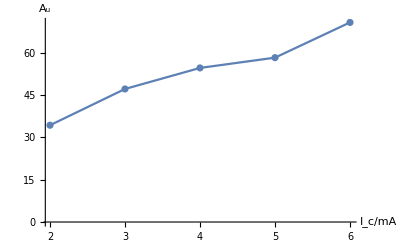

```mathematica
Show[ListPlot[Table[{ulist[[1,i]],(ulist[[2]]/ulist[[3]])[[i]]},{i,1,5}],AxesLabel->{"I_c/mA","A_u"}],ListLinePlot[Table[{ulist[[1,i]],(ulist[[2]]/ulist[[3]])[[i]]},{i,1,5}],AxesLabel->{"I_c/mA","A_u"}]]
```

```mathematica
MatrixForm[{Prepend[ulist[[1]],"Ic/mA"],Prepend[ulist[[2]],"Uppo/mV"],Prepend[ulist[[3]],"Uppi/mV"],Prepend[ulist[[2]]/ulist[[3]],"Au"]}]
```

(Ic/mA | 2 | 3 | 4 | 5 | 6
Uppo/mV | 632 | 680 | 700 | 700 | 680
Uppi/mV | 18.4 | 14.4 | 12.8 | 12. | 9.6
Au | 34.3478 | 47.2222 | 54.6875 | 58.3333 | 70.8333)

```mathematica
TableForm[{{"Ic/mA",2,3,4,5,6},{"Uppo/mV",632,680,700,700,680},{"Uppi/mV",18.4,14.4,12.8,12.,9.6},{"Au",34.34782608695652,47.22222222222222,54.6875,58.33333333333333,70.83333333333334}}]
```

Ic/mA | 2 | 3 | 4 | 5 | 6
Uppo/mV | 632 | 680 | 700 | 700 | 680
Uppi/mV | 18.4 | 14.4 | 12.8 | 12. | 9.6
Au | 34.3478 | 47.2222 | 54.6875 | 58.3333 | 70.8333

```mathematica
TableForm[{{34.34782608695652,47.22222222222222,54.6875,58.33333333333333,70.83333333333334}}]
```

34.3478 | 47.2222 | 54.6875 | 58.3333 | 70.8333

```mathematica
MatrixForm[{{34.34782608695652,47.22222222222222,54.6875,58.33333333333333,70.83333333333334}}]
```

(34.3478 | 47.2222 | 54.6875 | 58.3333 | 70.8333)

```mathematica
Grid[{{34.34782608695652,47.22222222222222,54.6875,58.33333333333333,70.83333333333334}}]
```

34.3478 | 47.2222 | 54.6875 | 58.3333 | 70.8333